```mathematica
{0.27,0.31,.18,.09,0.15}.{1,2,3,4,5}
```

2.54

```mathematica
{23,34,45,56,67}.{.1,0.45,0.19,0.09,0.17}
```

42.58

```mathematica
Table[(k-{23,34,45,56,67}.{0.1,0.45,0.19,0.09,0.17})^2,{k,{23,34,45,56,67}}]
```

{383.376,73.6164,5.8564,180.096,596.336}

```mathematica
Table[(k-{23,34,45,56,67}.{.1,0.45,0.19,0.09,0.17})^2,{k,{23,34,45,56,67}}].{0.1,0.45,0.19,0.09,0.17}
```

190.164

```mathematica
Sqrt[Table[(k-{23,34,45,56,67}.{.1,0.45,0.19,0.09,0.17})^2,{k,{23,34,45,56,67}}].{0.1,0.45,0.19,0.09,0.17}]
```

13.79

```mathematica
Total[{0.051,0.096,0.197,0.292,0.250,0.098,0.016}]
```

1.

```mathematica
GreatBritain1851FlorenceNightingaleNursesAgeProbabilities={0.051,0.096,0.197,0.292,0.250,0.098,0.016};
GreatBritain1851FlorenceNightingaleNurseAgeMidpoints={24.5,34.5,44.5,54.5,64.5,74.5,84.5};
```

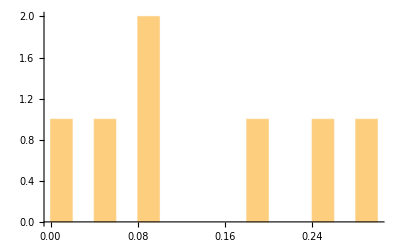

```mathematica
Histogram[GreatBritain1851FlorenceNightingaleNursesAgeProbabilities,9]
```

```mathematica
Total[GreatBritain1851FlorenceNightingaleNursesAgeProbabilities[[-3;;]]]
```

0.364

```mathematica
GreatBritain1851FlorenceNightingaleNurseAgeMidpoints.GreatBritain1851FlorenceNightingaleNursesAgeProbabilities
```

54.02

```mathematica
Sqrt[Table[(k-GreatBritain1851FlorenceNightingaleNurseAgeMidpoints.GreatBritain1851FlorenceNightingaleNursesAgeProbabilities)^2,{k,GreatBritain1851FlorenceNightingaleNurseAgeMidpoints}].GreatBritain1851FlorenceNightingaleNursesAgeProbabilities]
```

13.5044

```mathematica
0.01024 50000
```

512.

```mathematica
DeathBefore65YearsOldRetirementJimInsurance={0.01024,0.01339,0.01726,0.02011,0.02260};
```

```mathematica
DeathBefore65YearsOldRetirementJimInsurance 50000
```

{512.,669.5,863.,1005.5,1130.}

```mathematica
Total[DeathBefore65YearsOldRetirementJimInsurance 50000]
```

4180.

```mathematica
Total[DeathBefore65YearsOldRetirementJimInsurance 50000]+700
```

4880.

```mathematica
5000-Total[DeathBefore65YearsOldRetirementJimInsurance 50000]
```

820.

```mathematica
BinomialProbability[n_,r_,p_]:=
Binomial[n,r] p^r (1-p)^(n-r)
```

```mathematica
BinomialProbability[10,6,0.59]
```

0.250303

```mathematica
BinomialProbability[7,0,0.3]
```

0.0823543

```mathematica
1-BinomialProbability[7,0,0.3]
```

0.917646

```mathematica
BinomialProbability[4,4,.2]
```

0.0016

```mathematica
BinomialProbability[4,4,.8]
```

0.4096

```mathematica
BinomialProbability[10,6,0.59]
```

0.250303

```mathematica
Probability[x==6,x\[Distributed]BinomialDistribution[10,0.59]]
```

0.250303

```mathematica
Probability[x>=1,x\[Distributed]BinomialDistribution[4,0.2]]
```

0.5904

```mathematica
Probability[x>=2,x\[Distributed]BinomialDistribution[4,0.2]]
```

0.1808

```mathematica
Probability[x==0,x\[Distributed]BinomialDistribution[6,0.15]]
```

0.37715

```mathematica
Probability[#,x\[Distributed]BinomialDistribution[6,0.15]]&/@{x==0,x>=1,x<=2}
```

{0.37715,0.62285,0.952661}

```mathematica
Probability[#,x\[Distributed]BinomialDistribution[15,0.1]]&/@{x>=1,x>2,x==0,x<=2}
```

{0.794109,0.184061,0.205891,0.815939}

```mathematica
Total[{0.001405,0.014304,0.063716,0.162187,
0.258024,0.262716}]
```

0.762352

```mathematica
Total[{0.167183,0.060794,0.009672}]
```

0.237649

```mathematica
1-Total[{0.001405,0.014304,0.063716,0.162187,
0.258024,0.262716}]
```

0.237648

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[6,0.15]]&/@{x==0,x>=1,x<=2}
```

{0.9,0.9,0.9}

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[8,0.5]]
```

4.

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[8,0.9]]
```

7.2

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[8,0.9]]
```

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[7,0.7]]
```

4.9

```mathematica
StandardDeviation[BinomialDistribution[7,0.7]]
```

1.21244

```mathematica
4.9+2.5StandardDeviation[BinomialDistribution[7,0.7]]
```

7.93109

```mathematica
Expectation[x>=2,x\[Distributed]BinomialDistribution[4,0.7]]
```

0.0837 False+0.9163 True

```mathematica
Mean[BinomialDistribution[8,0.45]]
```

3.6

```mathematica
Round[StandardDeviation[BinomialDistribution[8,0.45]],0.01]
```

1.41

```mathematica
Round[Expectation[x==#,x\[Distributed]BinomialDistribution[4,0.75]][[2]]]&/@Range[0,4]
```

{Round[0.00390625 True],Round[0.046875 True],Round[0.210938 True],Round[0.421875 True],Round[0.316406 True]}

```mathematica
Mean[BinomialDistribution[4,0.75]]
```

3.

```mathematica
StandardDeviation[BinomialDistribution[4,0.25]]
```

0.866025

```mathematica
{#,Expectation[x>=3,x\[Distributed]BinomialDistribution[#,0.75]]}&/@Range[8]
```

{{1,1. False},{2,1. False},{3,0.578125 False+0.421875 True},{4,0.261719 False+0.738281 True},{5,0.103516 False+0.896484 True},{6,0.0375977 False+0.962402 True},{7,0.0128784 False+0.987122 True},{8,0.00422668 False+0.995773 True}}

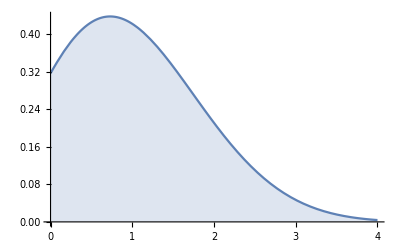

```mathematica
Plot[Evaluate@PDF[BinomialDistribution[4,0.25],x],{x,0,4},Filling->Axis]
```

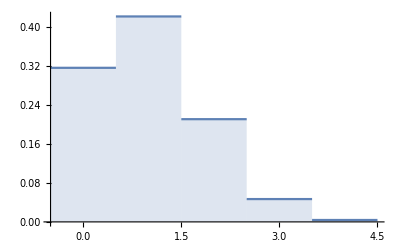

```mathematica
DiscretePlot[Evaluate@PDF[BinomialDistribution[4,0.25],x],{x,0,4},Filling->Axis,ExtentSize->Full]
```

```mathematica
{#,Expectation[x>=1,x\[Distributed]BinomialDistribution[#,0.60]]}&/@Range[8]
```

{{1,0.4 False+0.6 True},{2,0.16 False+0.84 True},{3,0.064 False+0.936 True},{4,0.0256 False+0.9744 True},{5,0.01024 False+0.98976 True},{6,0.004096 False+0.995904 True},{7,0.0016384 False+0.998362 True},{8,0.00065536 False+0.999345 True}}

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[7,0.60]]
```

4.2

```mathematica
Expectation[x==3,x\[Distributed]BinomialDistribution[3,0.15]]
```

0.996625 False+0.003375 True

```mathematica
Expectation[x<=1,x\[Distributed]BinomialDistribution[3,0.15]]
```

0.06075 False+0.93925 True

```mathematica
{#,Expectation[x>=1,x\[Distributed]BinomialDistribution[#,0.15]]}&/@Range[20]
```

{{1,0.85 False+0.15 True},{2,0.7225 False+0.2775 True},{3,0.614125 False+0.385875 True},{4,0.522006 False+0.477994 True},{5,0.443705 False+0.556295 True},{6,0.37715 False+0.62285 True},{7,0.320577 False+0.679423 True},{8,0.272491 False+0.727509 True},{9,0.231617 False+0.768383 True},{10,0.196874 False+0.803126 True},{11,0.167343 False+0.832657 True},{12,0.142242 False+0.857758 True},{13,0.120905 False+0.879095 True},{14,0.10277 False+0.89723 True},{15,0.0873542 False+0.912646 True},{16,0.0742511 False+0.925749 True},{17,0.0631134 False+0.936887 True},{18,0.0536464 False+0.946354 True},{19,0.0455994 False+0.954401 True},{20,0.0387595 False+0.96124 True}}

```mathematica
Expectation[#,x\[Distributed]BinomialDistribution[10,0.8]]&/@{x==10,x<=9,x}
```

{0.892626 False+0.107374 True,0.107374 False+0.892626 True,8.}

```mathematica
StandardDeviation[BinomialDistribution[10,.8]]
```

1.26491

```mathematica
{#,Expectation[x>=1,x\[Distributed]BinomialDistribution[#,0.2]]}&/@Range[20]
```

{{1,0.8 False+0.2 True},{2,0.64 False+0.36 True},{3,0.512 False+0.488 True},{4,0.4096 False+0.5904 True},{5,0.32768 False+0.67232 True},{6,0.262144 False+0.737856 True},{7,0.209715 False+0.790285 True},{8,0.167772 False+0.832228 True},{9,0.134218 False+0.865782 True},{10,0.107374 False+0.892626 True},{11,0.0858993 False+0.914101 True},{12,0.0687195 False+0.931281 True},{13,0.0549756 False+0.945024 True},{14,0.0439805 False+0.95602 True},{15,0.0351844 False+0.964816 True},{16,0.0281475 False+0.971853 True},{17,0.022518 False+0.977482 True},{18,0.0180144 False+0.981986 True},{19,0.0144115 False+0.985588 True},{20,0.0115292 False+0.988471 True}}

```mathematica
Expectation[x==9,x\[Distributed]BinomialDistribution[
9,0.95]]
```

0.369751 False+0.630249 True

```mathematica
Expectation[x==9,x\[Distributed]BinomialDistribution[
9,0.65]]
```

0.979288 False+0.0207119 True

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[
9,0.95]]
```

8.55

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[
9,0.65]]
```

5.85

```mathematica
StandardDeviation[BinomialDistribution[9,0.6]]
```

1.46969

```mathematica
StandardDeviation[BinomialDistribution[9,0.65]]
```

1.43091

```mathematica
{#,Expectation[x>=2,x\[Distributed]BinomialDistribution[#,0.65]]}&/@Range[20]
```

{{1,1. False},{2,0.5775 False+0.4225 True},{3,0.28175 False+0.71825 True},{4,0.126481 False+0.873519 True},{5,0.0540225 False+0.945978 True},{6,0.0223218 False+0.977678 True},{7,0.0090075 False+0.990992 True},{8,0.00357083 False+0.996429 True},{9,0.00139616 False+0.998604 True},{10,0.000539887 False+0.99946 True},{11,0.000206891 False+0.999793 True},{12,0.0000786876 False+0.999921 True},{13,0.0000297371 False+0.99997 True},{14,0.0000111768 False+0.999989 True},{15,4.18094×10^-6 False+0.999996 True},{16,1.5575×10^-6 False+0.999998 True},{17,5.78087×10^-7 False+0.999999 True},{18,2.13867×10^-7 False+1. True},{19,7.88912×10^-8 False+1. True},{20,2.90251×10^-8 False+1. True}}

```mathematica
{#,Expectation[x>=2,x\[Distributed]BinomialDistribution[#,0.95]]}&/@Range[20]
```

{{1,1. False},{2,0.0975 False+0.9025 True},{3,0.00725 False+0.99275 True},{4,0.00048125 False+0.999519 True},{5,0.00003 False+0.99997 True},{6,1.79688×10^-6 False+0.999998 True},{7,1.04688×10^-7 False+1. True},{8,5.97656×10^-9 False+1. True},{9,3.35938×10^-10 False+1. True},{10,1.86523×10^-11 False+1. True},{11,1.02539×10^-12 False+1. True},{12,5.59082×10^-14 False+1. True},{13,3.02734×10^-15 False+1. True},{14,1.62964×10^-16 False+1. True},{15,8.72803×10^-18 False+1. True},{16,4.65393×10^-19 False+1. True},{17,2.47192×10^-20 False+1. True},{18,1.30844×10^-21 False+1. True},{19,6.9046×10^-23 False+1. True},{20,3.6335×10^-24 False+1. True}}

```mathematica
Expectation[x==9,x\[Distributed]BinomialDistribution[9,0.60]]
```

0.989922 False+0.0100777 True

```mathematica
Round[0.0207119,0.001]
```

0.021

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[9,0.6]]
```

5.4

```mathematica
{#,Expectation[x>=2,x\[Distributed]BinomialDistribution[#,0.6]]}&/@Range[20]
```

{{1,1. False},{2,0.64 False+0.36 True},{3,0.352 False+0.648 True},{4,0.1792 False+0.8208 True},{5,0.08704 False+0.91296 True},{6,0.04096 False+0.95904 True},{7,0.0188416 False+0.981158 True},{8,0.00851968 False+0.99148 True},{9,0.00380109 False+0.996199 True},{10,0.00167772 False+0.998322 True},{11,0.000734003 False+0.999266 True},{12,0.000318767 False+0.999681 True},{13,0.000137573 False+0.999862 True},{14,0.0000590558 False+0.999941 True},{15,0.0000252329 False+0.999975 True},{16,0.0000107374 False+0.999989 True},{17,4.55267×10^-6 False+0.999995 True},{18,1.92415×10^-6 False+0.999998 True},{19,8.1089×10^-7 False+0.999999 True},{20,3.40849×10^-7 False+1. True}}

```mathematica
Mean[BinomialDistribution[4,0.75]]
```

3.

```mathematica
515./537
```

0.959032

```mathematica
Abs[0.95-515./537]
```

0.00903166

```mathematica
(3-3.1883)/0.1510
```

-1.24702

```mathematica
(3.4-3.1883)/0.1510
```

1.40199

```mathematica
-3(0.1510)+3.1883
```

2.7353

```mathematica
3(0.1510)+3.1883
```

3.6413